## Unit 5 Topics

## Initialization Cells

## Integrals

This code will compute any double integral and draw the region. I use Inactive[ ] so that I can see the integral setup to check that I typed things correctly.

1x01y01-x^2==2/3

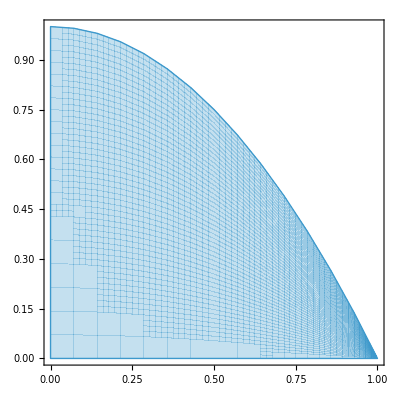

```mathematica
integrand=1;
oB={x,0,1};
iB={y,0,1-x^2};
coords={x,y};

areaIntegral =Inactive[Integrate][integrand,oB,iB];
areaIntegral ==Activate[areaIntegral]

ParametricPlot[coords, oB,iB]
```

```mathematica
Integrate[1,{x,0,1},{y,0,1-x^2}]
xbar = Integrate[x,{x,0,1},{y,0,1-x^2}]/Integrate[1,{x,0,1},{y,0,1-x^2}]
ybar = Integrate[y,{x,0,1},{y,0,1-x^2}]/Integrate[1,{x,0,1},{y,0,1-x^2}]
```

2/3

3/8

2/5

```mathematica
area=Integrate[r,{theta,0,Pi},{r,0,a}]
xbar =Integrate[(r Cos[theta])r,{theta,0,Pi},{r,0,a}]/area
ybar = Integrate[(r Sin[theta])r,{theta,0,Pi},{r,0,a}]/area
```

(a^2 π)/2

0

(4 a)/(3 π)

We can also compute center of mass.

```mathematica
density=1;
oB={x,0,a};
iB={y,0,b(1-x/a)};
coords={x,y};

massIntegral =Inactive[Integrate][density,oB,iB];
massIntegral ==Activate[massIntegral] 
xbar=Integrate[x density,oB,iB]/Integrate[density,oB,iB]
ybar=Integrate[y density,oB,iB]/Integrate[density,oB,iB]

ParametricPlot[coords, oB,iB]
```

1x0ay0b (1-x/a)==(a b)/2

a/3

b/3

ParametricPlot::plln: Limiting value a in {x,0,a} is not a machine-sized real number.

ParametricPlot[coords,oB,iB]

Now let’s try a polar coordinate problem

rtheta0πr05==(25 π)/2

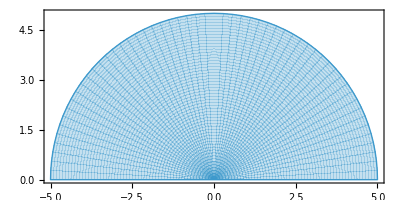

```mathematica
integrand=r;
oB={theta,0,Pi};
iB={r,0,5};
coords={r Cos[theta],r Sin[theta]};

areaIntegral =Inactive[Integrate][integrand,oB,iB];
areaIntegral ==Activate[areaIntegral]

ParametricPlot[coords, oB,iB]
```